# The Sandpile Model

Jonas Kaufman & Jon Ueki
Physics 170 SP16

## Introduction

The Sandpile Model, also known as the Bak-Tang-Wiesenfeld model (http://link.aps.org/doi/10.1103/PhysRevA.38.364), is a cellular automaton that aims to model “spatially extended dynamical systems.” The model displays self-organizing criticality, meaning that it always reaches a critical state without the fine tuning of any external parameter. The behavior of the critical state is characterized by spatial and temporal power laws and 1/f noise. This model has been extended to many systems beyond sandpiles, including earthquakes, the human brain, and how bills are passed in Congress. We are investigating how different initial conditions of the sandpile will affect what the critical state looks like.

## Graphics Setup

```mathematica
Module[{cmds= {"Plot", "ListPlot", "ListLinePlot", "ListLogPlot", "ListLogLogPlot","LogPlot","LogLogPlot","ListStepPlot"}},
For[j=1, j≤ Length[cmds],j++,SetOptions[Symbol[ cmds[[j]] ], Frame->True,LabelStyle->{Larger, FontFamily->"Utopia"}]]
]
```

## 1-D Model

### Rules

The model takes place on a row representing half a sandpile.
Each cell has height h_i and slope z_i where z_i=h_i-h_(i+1).
Adding a grain at cell i: z_i → z_i+1, z_(i-1) → z_(i-1)-1.
If z_i > z_c, cell “topples,” sending one grain of sand to the next cell down: z_i  → z_i- 2, z_(i±1) → z_(i±1) + 1.
Left boundary is closed whereas the right boundary is open .

### Initialization

The global variable row keeps track of the slope at each cell

```mathematica
length=20; (* length of row *)
zCrit1D=1;(* critical slope *)
randomRow[]:=row=Table[RandomInteger[zCrit],{length}] (* initialize row randomly *)
constantRow[c_]:=row=Table[c,{length}](* initialize row to constant slope *)
```

### Updating

relaxation1D relaxes the entire row until stable

```mathematica
relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit1D,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]
```

addGrain1D adds a grain of sand at a random cell

```mathematica
addGrain1D[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];
```

pourSand adds numGrains grains of sand and relaxes after each

```mathematica
pourSand[numGrains_]:=Module[{n,rows={row}},
For[n=1,n≤numGrains,n++,
addGrain1D[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]
```

### Simulation

If sand is added randomly to an empty row, the pile eventually reaches a critical state in which the slope at each cell is simply the critical slope.

```mathematica
constantRow[0];
rows=pourSand[650];
Animate[GraphicsColumn[{
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],FrameLabel->{"i","h"},Filling->Axis,PlotRange->{0,length*zCrit1D+1}],
ListStepPlot[rows[[t]],FrameLabel->{"i","z"},Filling->Axis,PlotRange->{-zCrit1D-1,zCrit1D+1}]
}],{t,1,Length[rows],1,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->Automatic]
```

## 2-D Model

#### Rules

The model takes place on a grid representing half a sandpile. 
“Slope” is z_(i,j)=2 h_(i,j)-h_(i+1,j)-h_(i,j+1).
Adding a grain at z_(i,j): z_(i,j) → z_(i,j)+2, z_(i-1,j) → z_(i-1,j)-1,  z_(i,j-1) → z_(i,j-1)-1
If z_(i,j) > z_c, cell “topples,” sending one grain down in each direction: z_(i,j) → z_(i,j)-4, z_(i±1,j) → z_(i±1,j)+1,  z_(i,j±1) → z_(i,j±1)+1
The top and left have closed boundary conditions, whereas the bottom and right have open boundary conditions.

#### Initialization

The global variable grid keeps track of the slope at each cell

```mathematica
gridSize = 20; (* side length of grid *)
zCrit = 2; (* the critical slope *)
randomGrid[]:=grid = Table[Table[RandomInteger[zCrit], {n, gridSize}], {n, gridSize}]; (* initialize grid randomly *)
constantGrid[c_]:=grid = Table[Table[c, {n, gridSize}], {n, gridSize}]; (* initialize grid to constant slope *)
```

#### Updating

relaxAll relaxes the entire grid until stable

```mathematica
relaxAll[]:=Module[{i,j,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ gridSize,i++,
For[j=1,j≤ gridSize,j++,
If[grid[[i,j]]> zCrit,
stable=False;
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
];
];
];
];
]
```

update relaxes a single cell and it’s neighbors (then their neighbors, etc.) until stable

```mathematica
update[ii_,jj_]:=Module[{stable=False,look={{ii,jj}},l,i,j},
While[!stable,
stable=True;
For[l=1,l≤ Length[look],l++,
{i,j}=look[[l]];
If[grid[[i,j]]>zCrit,
stable=False;
s++; (* count topple *)
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
(* relax neighbors *)
If[i≠1,AppendTo[look,{i-1,j}]];
If[j≠1,AppendTo[look,{i,j-1}]];
If[i≠gridSize,AppendTo[look,{i+1,j}]];
If[j≠gridSize,AppendTo[look,{i,j+1}]];
];
];
];
]
```

addSand adds a grain of sand at a specific or random place

```mathematica
addGrain[random_,place_] :=Module[{i, j}, 
If[random,(*If we activate random, then add grains randomly*)
i=RandomInteger[{1,gridSize}];j=RandomInteger[{1,gridSize}];,
i=place[[1]];j=place[[2]];
];
grid[[i,j]]+=2;
If[j≠1,grid[[i,j-1]]--];
If[i≠1,grid[[i-1,j]]--];
update[i,j];
]
```

run adds totalSand_ grains of sand (either randomly or at the center) and relaxes after each
returns a list of the grid at each time step and a list of the total number of topples each time step

```mathematica
run[totalSand_, random_:False,place_:{1,1}] := Module[{n,sList={},gList={}},
For[n=1,n≤ totalSand,n++,
s=0;(* keeps track of size of current avalanche *)
addGrain[random,place];
AppendTo[gList,grid];
AppendTo[sList,s];
];
{gList,sList}
]
```

#### Statistics

sDist produces a distribution of avalanche sizes from a list of avalanche sizes at each time step

```mathematica
sDist[sList_]:=Module[{dist=Table[0,{Max[sList]}],s,t},
For[t=1,t≤ Length[sList],t++,
s=sList[[t]];
If[s≠0,
dist[[s]]++
];
];
1./Length[sList] dist
]
```

#### Visualization

heights calculates an array of heights based on an array of slopes

```mathematica
heights[grid_]:=Module[{i,j,gridSize=Length[grid],heights},
heights=Table[Table[0, {gridSize}], {gridSize}];
For[i=gridSize-1,i> 0,i--,
For[j=gridSize-1,j> 0,j--,
heights[[i,j]]= 0.5(grid[[i,j]]+heights[[i+1,j]]+heights[[i,j+1]]);
];
];
heights
]
```

heightFull calculates an array of heights for the full sandpile based on one quarter of it

```mathematica
heightsFull[grid_]:=Module[{i,j,h,gridSize=Length[grid],heights},
heights=Table[Table[0, {n, 2*gridSize}], {n, 2*gridSize}];
For[i=gridSize-1,i≥0,i--,
For[j=gridSize-1,j≥0,j--,
h=0.5(If[i==0 || j==0,grid[[i+1,j+1]] ,grid[[i,j]]]
+ heights[[i+1 + gridSize,j + gridSize]]
+heights[[i + gridSize,j+1 + gridSize]]);
heights[[gridSize+i,gridSize+j]]=h;
heights[[gridSize+i, gridSize - j]] =h;
heights[[gridSize-i, gridSize+j]] = h;
heights[[gridSize-i, gridSize - j]] = h;
];
];
heights
]
```

Various functions to display simulation results and statistics:

```mathematica
dynamicGrids[]:=Dynamic[Grid[
{{ArrayPlot[grid,PlotLegends->Automatic,ColorFunction->GrayLevel, PlotLabel->"z",ImageSize->Medium],
ArrayPlot[heights[grid],PlotLegends->Automatic,ColorFunction->GrayLevel, PlotLabel->"h",ImageSize->Medium]}}
]];
```

```mathematica
sTimePlot[sList_]:=ListPlot[sList,PlotRange->All,Filling->Axis,FrameLabel->{t,s},ImageSize->Large];
```

```mathematica
sDistLogLogPlot[sList_,fit_]:=ListLogLogPlot[{sDist[sList],Table[a/x/.fit,{x,Length[sDist[sList]]}],Table[a x^b/.fit,{x,Length[sDist[sList]]}]},Joined->{False,True,True},FrameLabel->{"s","D(s)"},ImageSize->Large,PlotLegends->{"Results","a/s", "Fit"}]
```

```mathematica
sDistPlot[sList_,fit_]:=ListPlot[{sDist[sList],Table[a/x/.fit,{x,Length[sDist[sList]]}],Table[a x^b/.fit,{x,Length[sDist[sList]]}]},Joined->{False,True,True},FrameLabel->{"s","D(s)"},ImageSize->Large,PlotLegends->{"Results","a/s", "Fit"}]
```

```mathematica
zPlot[grid_]:=Histogram[Flatten[grid],Automatic, "Probability",AxesLabel->{"z","D(z)"}];
```

### Simulation and Results

#### Flat Surface Initialization

We start off with no grains of sand, meaning the slope everywhere is 0. Then we will run the simulation by adding 15,000 grains of sand randomly across the table.

```mathematica
constantGrid[0]; (*Initialize to no grains of sand*)
```

This shows a top down view of the sandpile. The left graph shows the slopes of the sandpile, the right shows the height of the sandpile. Note this only represents a quarter of the total sandpile.

```mathematica
dynamicGrids[]
```

```mathematica
{gList0,sList0}=run[15000, True]; (*Add 15k grains of sand*)
```

We can also visualize the pile in 3D, taking it to be symmetric about both axes.

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

This graph shows the avalanche size as a function of time. The avalache sizes appear random but with larger avalanches being less frequent. We also see the avalanches sizes are small initially, which makes sense as we are building the pile up from nothing.

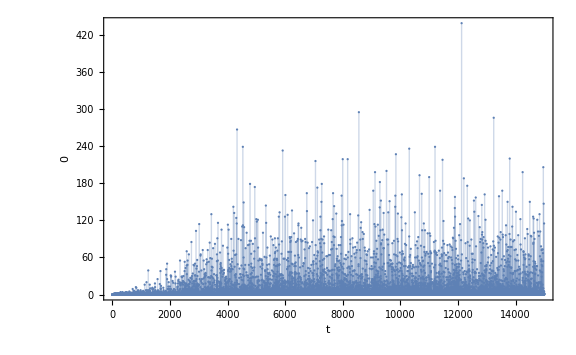

```mathematica
sTimePlot[sList0]
```

This log-log plot shows the distribution of avalanche sizes for the last 10,000 steps (allowing 5,000 steps to reach a critical state). This is a log-log plot where the x-axis is the size of the avalanche, and the y-axis is the frequency of that avalanche size. It is much more common to have smaller avalanches than larger ones. Though the fit shows a power law with power about -1.6, we can see from the graph above that the true exponent is somewhere between this and -1 (the power found by BTW). The resolution of this frequency plot, and therefore the quality of the fit, is limited by the number of time steps (sand grains) computed.

```mathematica
fit0=FindFit[sDist[sList0[[5000;;]]],a*x^b,{a,b},x]
```

{a→0.2792,b→-1.62841}

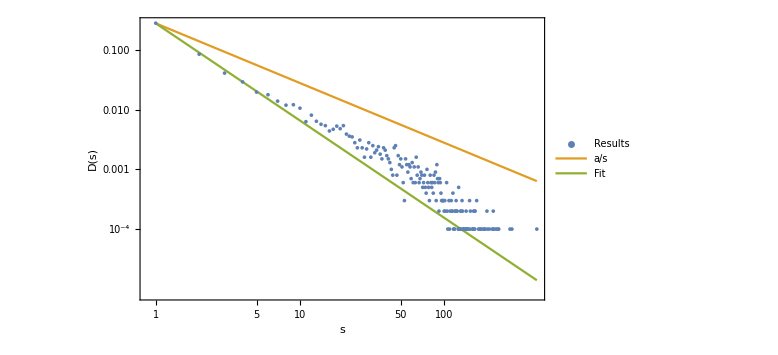

```mathematica
sDistLogLogPlot[sList0[[5000;;]],fit0]
```

We can also look at the average distrubtion of slopes over the last 10,000 steps. The distribution tends to higher slopes, but no slope is above the critical slope of 2. Also, the slopes do not converge to the critical slope like in 1D, since the avalanches can interact in two directions.

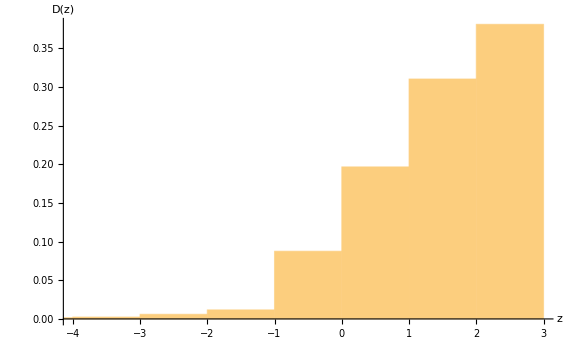

```mathematica
zPlot[gList0[[5000;;]]]
```

#### Critical Initialization

We could also begin with a sandpile in which every cell is at the critical slope of 2.

```mathematica
constantGrid[2];
```

Again, this shows the heights and slopes of the sandpile from a top-down point of view.

```mathematica
dynamicGrids[]
```

Again we drop 15,000 grains of sand.

```mathematica
{gList1,sList1}=run[15000, True];
```

Visualizing the pile in 3D:

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

Looking at the avalanche size as a function of time, we now see very large avalanches at first followed by random sizes. The initial behavior is that of the sandpile reaching a critical state.

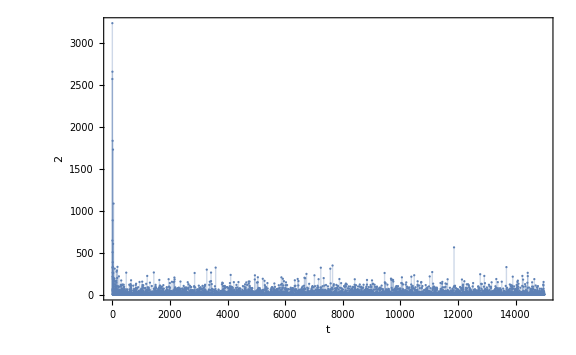

```mathematica
sTimePlot[sList1]
```

We see that the log-log plot of the distribution of avalanche sizes for the last 10,000 steps (allowing 5,000 steps to reach a critical state) looks similar to the previous case, with a power somewhere between -1.6 and -1.

```mathematica
fit1=FindFit[sDist[sList1[[5000;;]]],a*x^b,{a,b},x]
```

{a→0.293391,b→-1.65037}

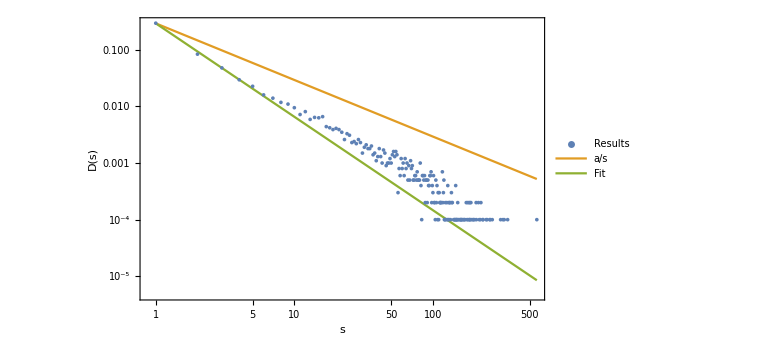

```mathematica
sDistLogLogPlot[sList1[[5000;;]],fit1]
```

The average distrubtion of slopes over the last 10,000 steps looks the same as before.

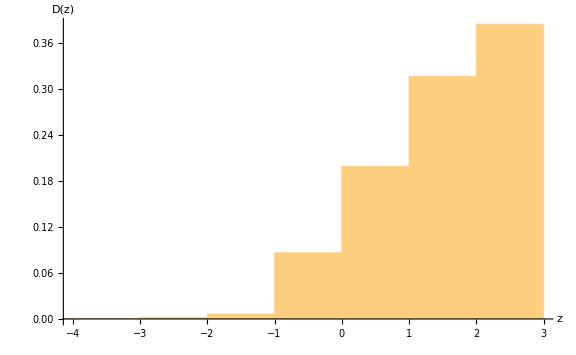

```mathematica
zPlot[gList1[[5000;;]]]
```

#### Supercritical Initialization

We could also begin with a sandpile in which every cell has slope 4, above the critical slope. First we relax the pile and then add 15,000 grains of sand randomly.

```mathematica
constantGrid[4];
```

Again, this shows the heights and slopes of the sandpile from a top-down point of view.

```mathematica
dynamicGrids[]
```

Relaxing the pile:

```mathematica
relaxAll[];
```

Again we drop 15,000 grains of sand.

```mathematica
{gList2,sList2}=run[15000, True];
```

Visualizing the pile in 3D:

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

Looking at the avalanche size as a function of time, we now see very large avalanches at first followed by random sizes. The initial behavior is that of the sandpile reaching a critical state.

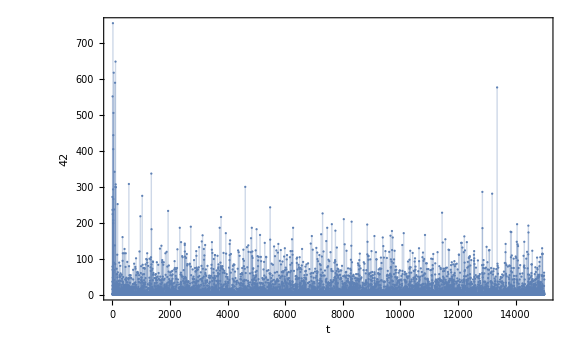

```mathematica
sTimePlot[sList2]
```

We see that the log-log plot of the distribution of avalanche sizes for the last 10,000 steps (allowing 5,000 steps to reach a critical state) looks similar to the previous case, with a power somewhere between -1.6 and -1.

```mathematica
fit2=FindFit[sDist[sList2[[5000;;]]],a*x^b,{a,b},x]
```

{a→0.280676,b→-1.58937}

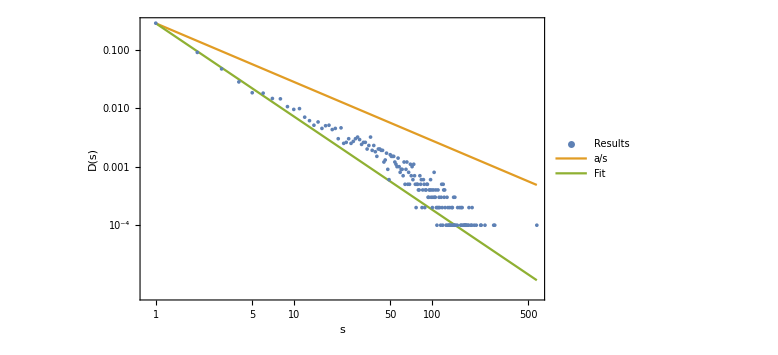

```mathematica
sDistLogLogPlot[sList2[[5000;;]],fit2]
```

The average distrubtion of slopes over the last 10,000 steps looks the same as before.

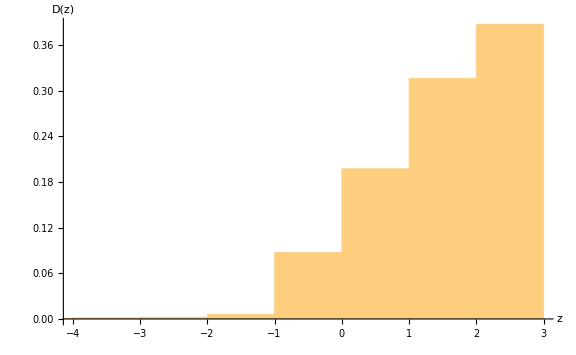

```mathematica
zPlot[gList2[[5000;;]]]
```

#### Comparing the three cases

Superimposing the avalanche size and slope distribution plots shows the behavior of the critical state appears to be the same in all three cases:

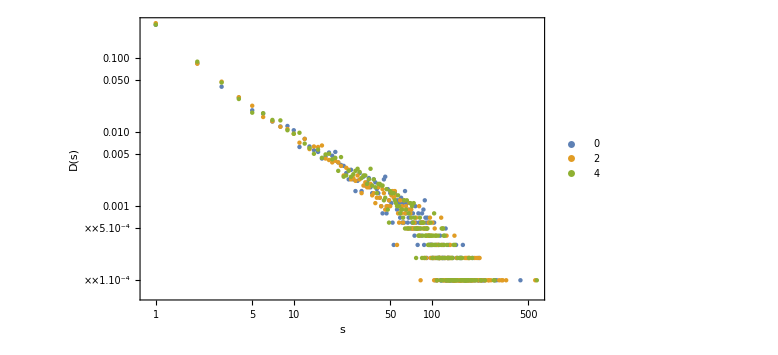

```mathematica
ListLogLogPlot[{sDist[sList0[[5000;;]]],sDist[sList1[[5000;;]]],sDist[sList2[[5000;;]]]},FrameLabel->{"s","D(s)"},ImageSize->Large,PlotLegends->{0,2,4}]
```

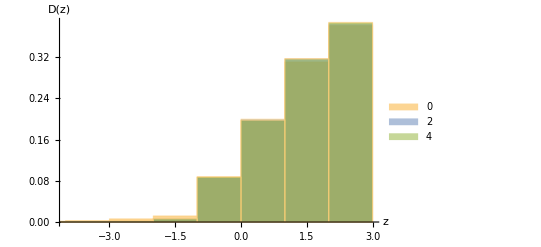

```mathematica
Histogram[{Flatten[gList0[[5000;;]]],Flatten[gList1[[5000;;]]],Flatten[gList2[[5000;;]]]},Automatic, "Probability",AxesLabel->{"z","D(z)"},ChartLegends->{0,2,4}]
```

#### Dropping at center

Though we were not as concerned with this case for our project, we could also start from an empty grid and drop sand only at the center point 1,1.
This is less interesting since it is non random, but it is how one might go about making a sand pile in real life.

```mathematica
constantGrid[0];
```

```mathematica
dynamicGrids[]
```

Adding 15,000 grains:

```mathematica
{gList3,sList3}=run[15000];
```

Visualizing the pile:

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

The slope distribution is peaked at 0 and looks different from our other cases.  We also notice that the pile does not extend to the boundaries of the table.

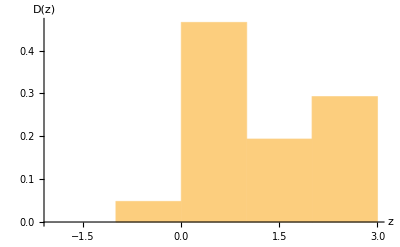

```mathematica
zPlot[gList3[[5000;;]]]
```

Adding 15,000 more grains, we see it looks a bit more like what we saw before.

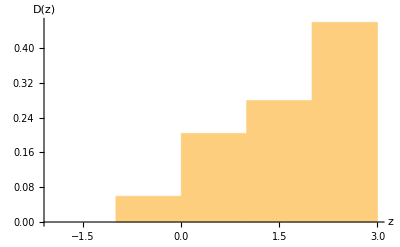

-Graphics3D-

```mathematica
{gList3,sList3}=run[15000];
zPlot[gList3[[5000;;]]]
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```